## Data

```mathematica
(* Initialize stuff *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["PMC`"];
Needs["GLSTools`"];
```

```mathematica
(* Read in data *)
vrad =SemanticImport["vrad_simu_challenge_inclination_90_1.rdb",ExcludedLines->{2}];
```

```mathematica
Keys[vrad][[1]]//Normal
```

{jdb,rv,sig_rv,fwhm,sig_fwhm,bis_span,sig_bis_span,rhk,sig_rhk,rv_osc_and_gran,rv_activity,rv_planet,rv_inst_noise,fwhm_osc_and_gran,fwhm_activity,fwhm_inst_noise,bis_span_osc_and_gran,bis_span_activity,bis_span_inst_noise,rhk_osc_and_gran,rhk_activity,rhk_inst_noise}

```mathematica
data = Normal@vrad[All,#]&/@ {"jdb",1000(#"rv_planet"+#"rv_inst_noise")&,1/(1000 #"sig_rv")^2&};
```

```mathematica
Clear[plot1];
plot1[logP_]:=ListPlot[Transpose[{FractionalPart[data[[1]]/Exp[logP]],data[[2]]}]]
```

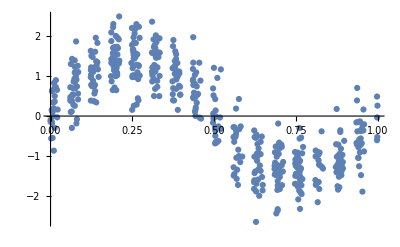

```mathematica
plot1[Log[16]]
```

```mathematica
ffreq = 2 Pi/Max@data[[1]];
```

```mathematica
freqs = Range[ffreq,0.5,ffreq];
```

```mathematica
pgram=GLS[data[[1]],data[[2]], data[[3]], freqs];
pfap = FAP[data[[1]],data[[2]], data[[3]],freqs,50];
```

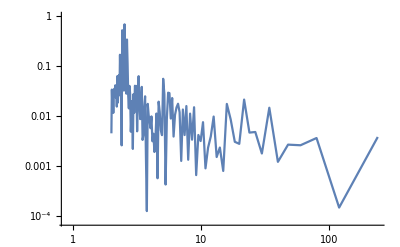

```mathematica
ListLogLogPlot[Transpose[{1/freqs,pgram}],Joined->True]
```

```mathematica
Quantile[pfap,0.95]
```

0.0124822

```mathematica
pgram[[10;;20]]
```

{0.00466939,0.0214768,0.00277718,0.00305159,0.00860102,0.017559,0.000793214,0.00234411,0.00151114,0.00980222,0.00391546}

```mathematica
1/freqs[[10;;20]]
```

{23.8747,21.7042,19.8956,18.3651,17.0533,15.9164,14.9217,14.0439,13.2637,12.5656,11.9373}

```mathematica
trials = Select[Transpose[{freqs,pgram}],#[[2]]>Quantile[pfap,0.95]&];
```

```mathematica
Length[trials]
```

59

## PMC step

```mathematica
Clear[rvmodel,chi2];
rvmodel[phi_,lfreq_,logK_]:=Module[{f,K=Exp[logK]},
f = 2 Pi (FractionalPart[data[[1]]Exp[lfreq]]+phi);
K Cos[f]
]
chi2[phi_?NumericQ,P_?NumericQ,logK_?NumericQ]:=Module[{rv},
rv = rvmodel[phi,P,logK];
Total[(data[[2]]- rv)^2*data[[3]]]
]
```

### Initialize

```mathematica
npop=10000;
mix = Table[{1.0,{0.5,Log[f1],0.0},DiagonalMatrix[{1.0,5*ffreq,1.0}]},{f1,trials[[All,1]]}];
model= buildModels@mix;
eps = DiagonalMatrix[{0.1,0.01,0.1}^2];
Clear[fiddle];
fiddle[x_,y_,z_] := {Mod[x,1],y,z};
fiddle[-0.9,10,10]
```

{0.1,10,10}

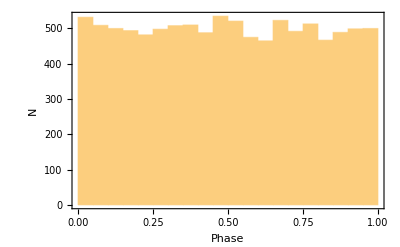

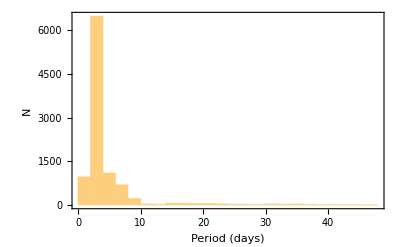

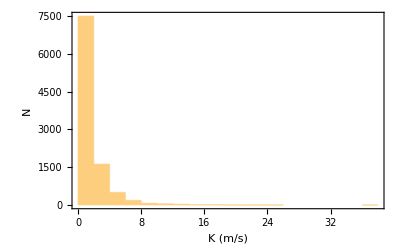

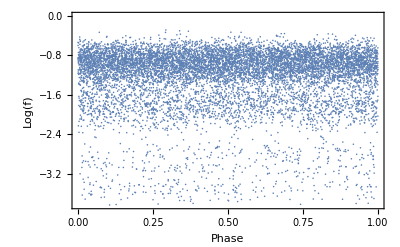

```mathematica
xx = mkRandom[model,npop, fiddle]; (* One off for simplicity *)
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[Exp[-xx[[All,2]]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Log(f)"}]
```

#### The PMC Loop

```mathematica
(* The PMC loop starts here, execute this cell until the perplexity
gets close to 1 *)
{perplex,xx,model}=iterPMC[chi2,npop,model,eps,fiddle,100];
perplex
Mean[MixtureDistribution@@model]
StandardDeviation[MixtureDistribution@@model]
```

Iteration:0 0.0001 {0.785448,-2.77095,-0.0493471}

Number of components:8

Iteration:1 0.0001 {0.724766,-2.77225,0.191702}

Number of components:8

Iteration:2 0.000150269 {0.758449,-2.77274,0.349932}

Number of components:8

Iteration:3 0.000830122 {0.745037,-2.77248,0.404541}

Number of components:8

Iteration:4 0.000847787 {0.748947,-2.77252,0.413408}

Number of components:8

Iteration:5 0.00089918 {0.746594,-2.77253,0.387706}

Number of components:8

Iteration:6 0.00125098 {0.742266,-2.77246,0.395975}

Number of components:8

Iteration:7 0.00151124 {0.742535,-2.77247,0.393648}

Number of components:8

Iteration:8 0.00215265 {0.744674,-2.77249,0.396341}

Number of components:8

Iteration:9 0.00335821 {0.745967,-2.77252,0.393646}

Number of components:8

Iteration:10 0.00481956 {0.744249,-2.77249,0.400315}

Number of components:8

Iteration:11 0.00501937 {0.745976,-2.77252,0.395336}

Number of components:8

Iteration:12 0.00579826 {0.744352,-2.77249,0.396651}

Number of components:8

Iteration:13 0.00772528 {0.745718,-2.77251,0.3983}

Number of components:8

Iteration:14 0.00896427 {0.745218,-2.7725,0.398191}

Number of components:8

Iteration:15 0.0130289 {0.745809,-2.77251,0.401429}

Number of components:8

Iteration:16 0.0145504 {0.74432,-2.7725,0.394492}

Number of components:8

Iteration:17 0.0181731 {0.744307,-2.7725,0.396453}

Number of components:8

Iteration:18 0.0220531 {0.74552,-2.77251,0.401549}

Number of components:8

Iteration:19 0.0256195 {0.744825,-2.7725,0.397813}

Number of components:8

Iteration:20 0.0302929 {0.744988,-2.7725,0.398063}

Number of components:8

Iteration:21 0.0360406 {0.745236,-2.7725,0.395026}

Number of components:8

Iteration:22 0.040543 {0.745428,-2.77251,0.398378}

Number of components:8

Iteration:23 0.0511372 {0.745021,-2.7725,0.395824}

Number of components:8

Iteration:24 0.0589812 {0.745102,-2.77251,0.395838}

Number of components:8

Iteration:25 0.0685392 {0.745087,-2.77251,0.396637}

Number of components:8

Iteration:26 0.0752246 {0.745168,-2.77251,0.397206}

Number of components:8

Iteration:27 0.0873222 {0.744989,-2.7725,0.395979}

Number of components:8

Iteration:28 0.0974472 {0.744913,-2.7725,0.396799}

Number of components:8

Iteration:29 0.111365 {0.745011,-2.7725,0.397849}

Number of components:8

Iteration:30 0.121372 {0.745139,-2.7725,0.398105}

Number of components:8

Iteration:31 0.133127 {0.744989,-2.7725,0.396513}

Number of components:8

Iteration:32 0.154655 {0.744963,-2.7725,0.395819}

Number of components:8

Iteration:33 0.166312 {0.745144,-2.7725,0.396523}

Number of components:8

Iteration:34 0.181785 {0.745058,-2.7725,0.396375}

Number of components:8

Iteration:35 0.206319 {0.745076,-2.7725,0.395694}

Number of components:8

Iteration:36 0.228064 {0.745007,-2.7725,0.396648}

Number of components:8

Iteration:37 0.24303 {0.745121,-2.7725,0.39587}

Number of components:8

Iteration:38 0.264943 {0.74484,-2.7725,0.39634}

Number of components:8

Iteration:39 0.288661 {0.745236,-2.77251,0.395712}

Number of components:8

Iteration:40 0.313481 {0.744974,-2.7725,0.395826}

Number of components:8

Iteration:41 0.353289 {0.745204,-2.7725,0.396458}

Number of components:8

Iteration:42 0.371519 {0.744843,-2.7725,0.396617}

Number of components:8

Iteration:43 0.408315 {0.744954,-2.7725,0.396206}

Number of components:8

Iteration:44 0.443072 {0.744931,-2.7725,0.396447}

Number of components:8

Iteration:45 0.482202 {0.745065,-2.7725,0.396388}

Number of components:8

Iteration:46 0.520799 {0.744917,-2.7725,0.396106}

Number of components:8

Iteration:47 0.556425 {0.74509,-2.7725,0.39614}

Number of components:8

Iteration:48 0.597701 {0.745018,-2.7725,0.396683}

Number of components:8

Iteration:49 0.630676 {0.744839,-2.7725,0.396234}

Number of components:8

Iteration:50 0.679055 {0.745016,-2.7725,0.396272}

Number of components:8

Iteration:51 0.707689 {0.744945,-2.7725,0.396432}

Number of components:8

Iteration:52 0.74647 {0.744995,-2.7725,0.395818}

Number of components:8

Iteration:53 0.780179 {0.744913,-2.7725,0.396691}

Number of components:8

Iteration:54 0.815026 {0.744942,-2.7725,0.396311}

Number of components:8

Iteration:55 0.8451 {0.745051,-2.7725,0.396255}

Number of components:8

Iteration:56 0.873728 {0.745076,-2.7725,0.396513}

Number of components:8

Iteration:57 0.897782 {0.744851,-2.7725,0.396567}

Number of components:8

Iteration:58 0.916086 {0.744891,-2.7725,0.396484}

Number of components:8

Iteration:59 0.935121 {0.744834,-2.7725,0.396583}

Number of components:8

Iteration:60 0.946543 {0.744977,-2.7725,0.39642}

Number of components:8

Iteration:61 0.960101 {0.744963,-2.7725,0.396512}

Number of components:8

0.960101

{0.744963,-2.7725,0.396512}

{0.00766718,0.000132789,0.0205641}

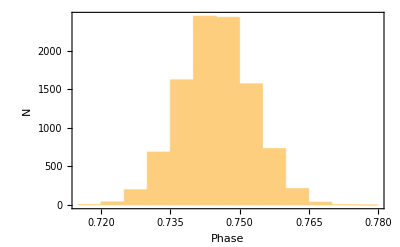

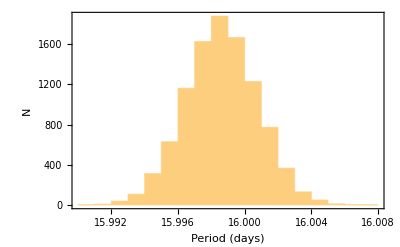

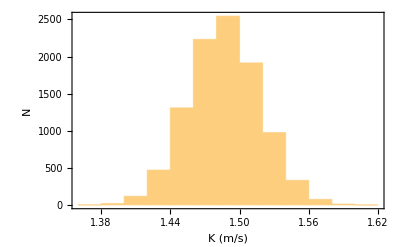

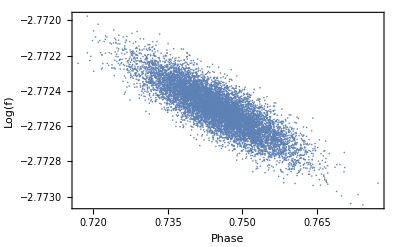

```mathematica
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[Exp[-xx[[All,2]]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Log(f)"}]
```